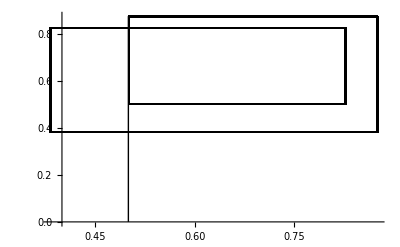

```mathematica
Remove["Global`*"]
(*Logistics Equation from Chaos Theory*)
α=3.5;
x[1]=0.5;
nmax=150;

f[x_]=α x (1-x);
x[n_]:=x[n]=α x[n-1] (1 - x[n-1]);

xlist=Flatten[Table[{{x[n],x[n+1]},{x[n+1],x[n+1]}},{n,1,nmax}],1];
xlist=Prepend[xlist,{x[1],0}];

curve:=Plot[α x (1-x),{x,0,1},PlotStyle->{Blue}]
mirror:=Plot[x,{x,0,1},PlotStyle->{Red}]
steps:=ListLinePlot[xlist,PlotStyle->{Black}]
steps
```